# Approximating Pi

## ACM40960 Project by Peter Adye Curran and Ellen Bennett

## Method 1 - Archimedes’ Method

### Illustrating the Approximation Method using a Manipulate Function

```mathematica
(* Create a Manipulate function for a range of values of n, where n is the number of sides of the polygon. Locally define the variables 'bigpoly', 'smallpoly', 'bigestimate', and 'smallstimate' using the Module function. *)
Manipulate[Module[{bigpoly, smallpoly, bigestimate, smallestimate},

(* Define the variable 'bigpoly' to be a polygon with n sides and a radius of 1/(Cos[180]/n) degrees. *)
bigpoly = RegularPolygon[1/Cos[180/n Degree],n];

(* Define the variable 'smallpoly' to be a polygon with n points on the unit circle. *)
smallpoly=Polygon[CirclePoints[1,n]];

(* Define the two estimates of Pi using Tan and Sin. *)
bigestimate = n Tan[180/n Degree];
smallestimate = n Sin[180/n Degree];

(* Display both of the polygons along with the unit circle, using differing colours and outlines. *)
Show[{Graphics[{Opacity[0.15],EdgeForm[Directive[Thick, Dashed, Blue]],Blue, Rotate[smallpoly, 90 Degree]}], 

			    Graphics[{Opacity[0.15],EdgeForm[Directive[Thick, Dashed, Red]],Red, bigpoly, Opacity[0.15]}]},

			      Graphics[Circle[{0,0}]], ImageSize->Medium, Axes->True]],

{n, {6,12,24,48,96}}]
```

### Approximation Results and Convergence

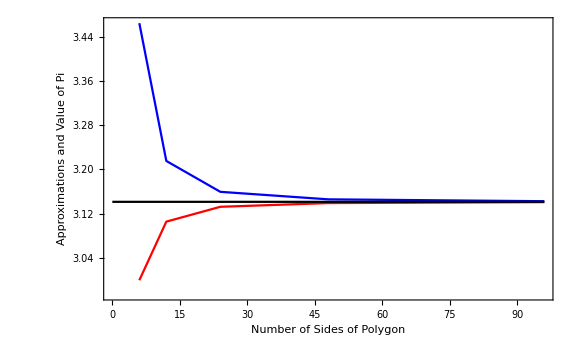

```mathematica
GraphicsRow[

(* Create two tables of two dimensional coordinates, where the x coordinate is n, the number of sides, and the y coordinate is the numerical value of the perimeter of the circumscribed, and iscribed polygons.*)
{Show[ListLinePlot[{Table[{n,N[n Sin[180/n Degree]]},{n,{6,12,24,48,96}}],Table[{n,N[n Tan[180/n Degree]]},{n,{6,12,24,48,96}}]},

(* Specify desired colours and plot a horizontal line for the true value of Pi. *)
PlotStyle->{Red,Blue}],Plot[π,{x,0,96},PlotStyle->Black], 

       (* Include a frame and specify the and axes labels, as well as the size of the plot. *)
Frame->True,FrameLabel->{"Number of Sides of Polygon \n ","  \n Approximations and Value of Pi"},RotateLabel->True,ImageSize->Large,LabelStyle->Directive[Bold,Black]],

	(* Add a legend to the plot. *)
LineLegend[{Blue,Black,Red},{"Circumscribed Polygon","Inscribed Polygon","Pi"}]}]
```

## Method 3 - Quadrant Method

### Illustrate Areas

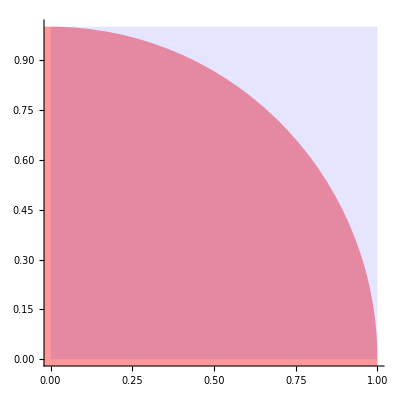

```mathematica
(* Plot a unit square and a quadrant of the unit circle. Use different colours to distinguish the areas. Show the x and y axes. *)
Show[Graphics[{Opacity[0.4],Red,Disk[{0,0},1]}],Graphics[{Opacity[0.1],Blue,Rectangle[]}],PlotRange->{{0,1},{0,1}},Axes->True]
```

### Demonstrate the Method Using a Manipulate Function

```mathematica
Manipulate[
(* Use the RandomPoint[] function to generate a list of n pseudorandom points uniformly distributed in the region Rectangle[]. Rectangle[] is equivalent to a unit square. *)
points = RandomPoint[Rectangle[],n];

(* RegionMember[] gives True if the point is a member of the region Disk[{0,0},1], which is a disk of radius 1 with centre at {0,0}. *)
inside = RegionMember[Disk[{0,0},1]];

(* Pick out the elements of the list of points for which inside[points] is True, i.e. which points are inside of the disk. Colour these select points red. *)
Show[Graphics[{Point[points],Red,Point[Pick[points,inside[points]]],AbsolutePointSize[3]}],Graphics[Circle[{0,0}], Axes->True],

(* Show the unit square in blue. *)
Graphics[{Opacity[0.1],Blue,Rectangle[]}],PlotRange->{{0,1},{0,1}},

(* Print the approximated value of Pi as the title of the plot. *)
PlotLabel->N[(Length[Pick[points,inside[points]]]/Length[points])4,4],LabelStyle->Directive[Bold,Black],Axes->True],

(* Specify the values of n to be used. *)
{n,{10^2,10^3,10^4,10^5}}]
```

### Three Trials for Different Seeds and Error Bars

```mathematica
list1 = List[];SeedRandom[100];
table1=Table[x=RandomReal[];y=RandomReal[];
If[x^2+y^2<=1,list1=Append[list1,1],list1=Append[list1,0]];
4 Total[list1]/Length[list1],{n,1,10^5}];
```

```mathematica
list2 = List[];SeedRandom[200];
table2=Table[x=RandomReal[];y=RandomReal[];
If[x^2+y^2<=1,list2=Append[list2,1],list2=Append[list2,0]];
4 Total[list2]/Length[list2],{n,1,10^5}];
```

$Aborted

```mathematica
list1 = List[];SeedRandom[200];
table2=Table[x=RandomReal[];y=RandomReal[];
If[x^2+y^2<=1,list1=Append[list1,1],list1=Append[list1,0]];
4Total[list1],{n,1,10^5}];
```

```mathematica
SeedRandom[333];
tab3=Table[points = RandomPoint[Rectangle[],n];
inside = RegionMember[Disk[{0,0},1]];
N[(Length[Pick[points,inside[points]]]/Length[points])4,4],
{n,1,10^5}];
```

```mathematica
average = (tab1+tab2+tab3)/3;
```

```mathematica
means={{10^2,average[[10^2]]},{10^3,average[[10^3]]},{10^4,average[[10^4]]},{10^5,Last[average]}};
```

```mathematica
sd1={StandardDeviation[average[[1;;10^2]]],StandardDeviation[average[[1;;10^3]]], StandardDeviation[average[[1;;10^4]]], StandardDeviation[average]};
```

$Aborted

```mathematica
sd2=Times[sd1,2];
```

```mathematica
errors1={{10^2,average[[10^2]]+sd1[[1]]},{10^3,average[[10^3]]+sd1[[2]]},{10^4,average[[10^4]]+sd1[[3]]},{10^5,Last[average]+sd1[[4]]},
{10^2,average[[10^2]]-sd1[[1]]},{10^3,average[[10^3]]-sd1[[2]]},{10^4,average[[10^4]]-sd1[[3]]},{10^5,Last[average]-sd1[[4]]}};
```

```mathematica
errors2={{10^2,average[[10^2]]+sd2[[1]]},{10^3,average[[10^3]]+sd2[[2]]},{10^4,average[[10^4]]+sd2[[3]]},{10^5,Last[average]+sd2[[4]]},
{10^2,average[[10^2]]-sd2[[1]]},{10^3,average[[10^3]]-sd2[[2]]},{10^4,average[[10^4]]-sd2[[3]]},{10^5,Last[average]-sd2[[4]]}};
```

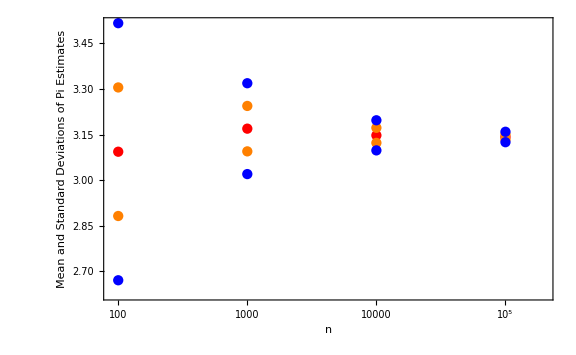

```mathematica
GraphicsRow[{ListPlot[{means,errors1, errors2},ScalingFunctions->{"Log"}, 
ImageSize->Large, PlotRange->{{90,200000},Full}, PlotStyle->{Red, Orange, Blue},
Frame->True,FrameLabel->{"n","  \n Mean and Standard Deviations of Pi Estimates"},
RotateLabel->True,LabelStyle->Directive[Black,Bold]],
PointLegend[{Red,Orange,Blue},{"Mean of Estimate","One Sigma Error Bars","Two Sigma Error Bars"}]}]
```

### Relative Difference Plots

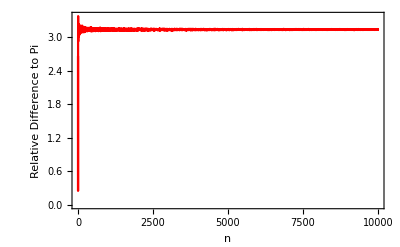

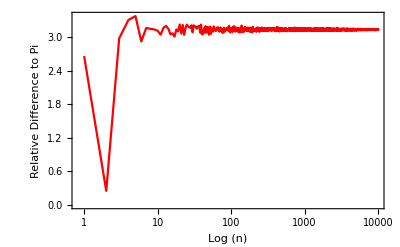

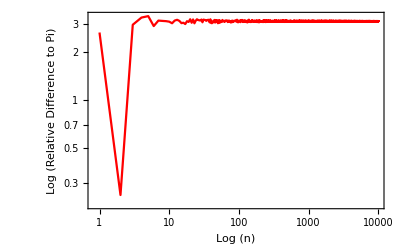

```mathematica
relativediff=MapAt[Abs[#-π]&,average,All];

ListLinePlot[relativediff,PlotRange->Full ,PlotStyle->Red,
Frame->True,FrameLabel->{"n","  \n Relative Difference to Pi"},
RotateLabel->True, LabelStyle->Directive[Black,Bold]]
ListLinePlot[relativediff,PlotRange->Full ,PlotStyle->Red,
ScalingFunctions->{"Log"},
Frame->True,FrameLabel->{"Log (n)","  \n Relative Difference to Pi"},
RotateLabel->True, LabelStyle->Directive[Black,Bold]]
ListLinePlot[relativediff,PlotRange->Full ,PlotStyle->Red,
ScalingFunctions->{"Log","Log"},
Frame->True,FrameLabel->{"Log (n)","  \n Log (Relative Difference to Pi)"},
RotateLabel->True, LabelStyle->Directive[Black,Bold]]
```

### Rough Work

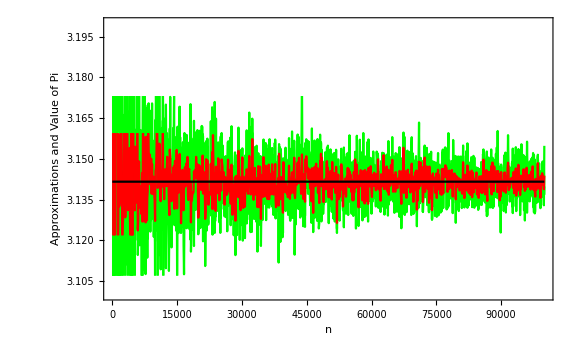

```mathematica
GraphicsRow[{Show[

(* Create a plot of table values, joined together by lines. *)
ListLinePlot[{

(* Create three tables of length n that compute the proportion of randomly generated points that are contained within the quadrant, and then multiply it by four. *)
SeedRandom[111];
tab1=Table[{n,points = RandomPoint[Rectangle[],n];

(* The number of points range from 10^2 to 10^5 with step size equal to 2000. *)
inside = RegionMember[Disk[{0,0},1]];N[(Length[Pick[points,inside[points]]]/Length[points])4,4]},{n,10^2,10^5,100}],

SeedRandom[222];
tab2=Table[{n,points = RandomPoint[Rectangle[],n];
inside = RegionMember[Disk[{0,0},1]];N[(Length[Pick[points,inside[points]]]/Length[points])4,4]},{n,10^2,10^5,100}],

SeedRandom[333];
tab3=Table[{n,points = RandomPoint[Rectangle[],n];
inside = RegionMember[Disk[{0,0},1]];

(* Colour the lines green. *)
N[(Length[Pick[points,inside[points]]]/Length[points])4,4]},{n,10^2,10^5,100}]},PlotStyle->Green],

(* Plot the average of the values from the three tables. Colour this line red. *)
ListLinePlot[avg=(tab1+tab2+tab3)/3,PlotStyle->Red],

(* Include the true value of Pi as a black horizontal line. Assign labels to the axes. *)
Plot[π,{x,0,10^5},PlotStyle->Black],ImageSize->Large,Frame->True,
FrameLabel->{"n","  \n Approximations and Value of Pi"},RotateLabel->True,
ImageSize->Large,LabelStyle->Directive[Black,Bold],
PlotRange->{{0,100000},{3.1,3.2}}],

	(* Add a legend to the plot. *)
LineLegend[{Green,Red,Black},{"Trials 1 - 3","Mean of the Trials","Pi"}]}]
```

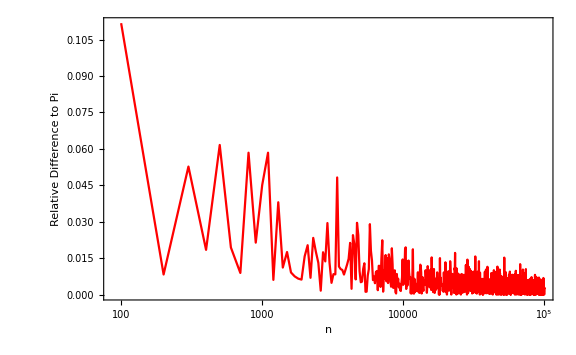

```mathematica
relativediff=MapAt[Abs[#-π]&,avg,{All,2}];

ListLinePlot[relativediff,PlotRange->Full ,PlotStyle->Red,ScalingFunctions->{"Log"},
Frame->True,FrameLabel->{"n","  \n Relative Difference to Pi"},
RotateLabel->True, LabelStyle->Directive[Black,Bold], ImageSize->Large]
```

```mathematica
Needs["ErrorBarPlots`"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
errors={#2,Abs[#2-π]}&@@@avg;
```

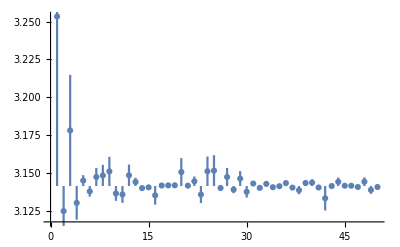

```mathematica
ErrorListPlot[errors,PlotRange->Full]
```

## Method 5 - Gamma Function Integral

### Function to Approximate Pi

```mathematica
gamma[n_]:={Quiet[(* Mute messages. *)

estimates1=List[];SeedRandom[100]; (* Create an empty list and set a random seed. *)
For[i=1,i<n+1,i++, (* Create a For loop from 1 to n. *)
u=RandomReal[]; (* Compute a random number in the range [0,1]. *)
integral=E^(1-1/u)/(u^2 √(1/u-1)); (* Compute the relevant expression. *)
estimates1=Append[estimates1,integral]];
approx1 = Mean[estimates1]^2 ;(* Add this evaluated expression to the list. *)(* Compute the mean of the estimates and square it. *)


estimates2=List[];SeedRandom[200]; (* Repeat for a new seed. *)
For[i=1,i<n+1,i++, 
u=RandomReal[];
integral=E^(1-1/u)/(u^2 √(1/u-1)); 
estimates2=Append[estimates2,integral]];
approx2 = Mean[estimates2]^2;


estimates3=List[];SeedRandom[300]; (* Repeat for a new seed. *)
For[i=1,i<n+1,i++, 
u=RandomReal[];
integral=E^(1-1/u)/(u^2 √(1/u-1)); 
estimates3=Append[estimates3,integral]];
approx3 = Mean[estimates3]^2;


mean=(approx1 +approx2+approx3)/3]} (* Compute the mean of the three separate means. *)
```

```mathematica
gammaestimates=Table[{n,gamma[n]},{n,{10^2,10^3,10^4,10^5}}]
```

{{100,{3.34248}},{1000,{3.17582}},{10000,{3.0081}},{100000,{3.14692}}}

### Computing Error Bars

```mathematica
Quiet[(* Mute error messages. *)

estimates=List[];SeedRandom[100]; (* Create an empty list and set a random seed. *)
tab1=Table[u=RandomReal[];integral=E^(1-1/u)/(u^2 √(1/u-1)); (* Create a table of coordinates where the x coordinate is the current number of iterations, and the y coordinate is the squared mean for 1 to n of the expression evaluated for a random value of u in the range [0,1]. *)
estimates=Append[estimates,integral];Mean[estimates]^2,{n,1,10^5}];

	(* Repeat for two more different random seeds. *)
estimates=List[];SeedRandom[200];
tab2=Table[u=RandomReal[];integral=E^(1-1/u)/(u^2 √(1/u-1));
estimates=Append[estimates,integral];Mean[estimates]^2,{n,1,10^5}];

estimates=List[];SeedRandom[300];
tab3=Table[u=RandomReal[];integral=E^(1-1/u)/(u^2 √(1/u-1));
estimates=Append[estimates,integral];Mean[estimates]^2,{n,1,10^5}];]

(* Compute the mean of all of the estimates. *)
average=(tab1+tab2+tab3)/3;
```

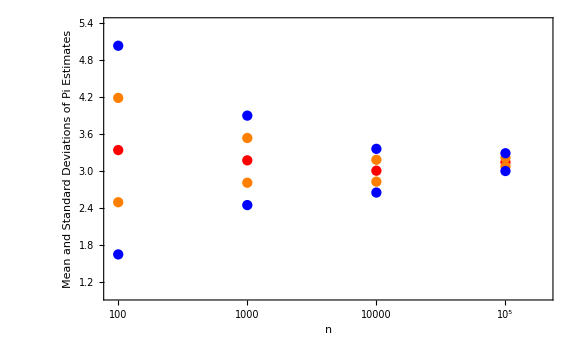

```mathematica
means={{10^2,average[[10^2]]},{10^3,average[[10^3]]},{10^4,average[[10^4]]},{10^5,Last[average]}};
sd1={StandardDeviation[average[[1;;10^2]]],StandardDeviation[average[[1;;10^3]]], StandardDeviation[average[[1;;10^4]]], StandardDeviation[average]};
sd2=Times[sd1,2];
errors1={{10^2,average[[10^2]]+sd1[[1]]},{10^3,average[[10^3]]+sd1[[2]]},{10^4,average[[10^4]]+sd1[[3]]},{10^5,Last[average]+sd1[[4]]},
{10^2,average[[10^2]]-sd1[[1]]},{10^3,average[[10^3]]-sd1[[2]]},{10^4,average[[10^4]]-sd1[[3]]},{10^5,Last[average]-sd1[[4]]}};
errors2={{10^2,average[[10^2]]+sd2[[1]]},{10^3,average[[10^3]]+sd2[[2]]},{10^4,average[[10^4]]+sd2[[3]]},{10^5,Last[average]+sd2[[4]]},
{10^2,average[[10^2]]-sd2[[1]]},{10^3,average[[10^3]]-sd2[[2]]},{10^4,average[[10^4]]-sd2[[3]]},{10^5,Last[average]-sd2[[4]]}};
GraphicsRow[{ListPlot[{means,errors1, errors2},ScalingFunctions->{"Log"}, 
ImageSize->Large, PlotRange->{{90,200000},{1,5.4}}, PlotStyle->{Red, Orange, Blue},
Frame->True,FrameLabel->{"n","  \n Mean and Standard Deviations of Pi Estimates"},
RotateLabel->True,LabelStyle->Directive[Black,Bold]],
PointLegend[{Red,Orange,Blue},{"Mean of Estimate","One Sigma Error Bars","Two Sigma Error Bars"}]}]
```

### Relative Difference to Pi

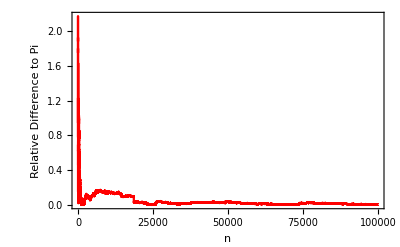

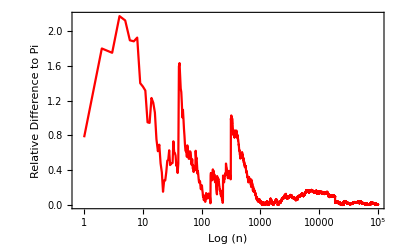

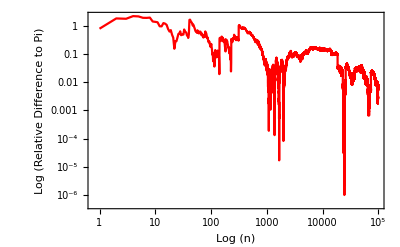

```mathematica
relativediff=MapAt[Abs[#-π]&,average,All];

ListLinePlot[relativediff,PlotRange->Full ,PlotStyle->Red,
Frame->True,FrameLabel->{"n","  \n Relative Difference to Pi"},
RotateLabel->True, LabelStyle->Directive[Black,Bold]]
ListLinePlot[relativediff,PlotRange->Full ,PlotStyle->Red,
ScalingFunctions->{"Log"},
Frame->True,FrameLabel->{"Log (n)","  \n Relative Difference to Pi"},
RotateLabel->True, LabelStyle->Directive[Black,Bold]]
ListLinePlot[relativediff,PlotRange->Full ,PlotStyle->Red,
ScalingFunctions->{"Log","Log"},
Frame->True,FrameLabel->{"Log (n)","  \n Log (Relative Difference to Pi)"},
RotateLabel->True, LabelStyle->Directive[Black,Bold]]
```

### Convergence Plot

```mathematica
(* Plot the estimates along with the mean estimate, and the true value of Pi. *)
GraphicsRow[{Show[ListLinePlot[{tab1,tab2,tab3},PlotRange->{{0,10^5},{2.7,3.5}},PlotStyle->Green],
ListLinePlot[average,PlotStyle->Red],Plot[π,{x,0,10^5},PlotStyle->Black],
ImageSize->Large,Frame->True,FrameLabel->{"n","  \n Approximations and Value of Pi"},
RotateLabel->True,ImageSize->Large,LabelStyle->Directive[Black,Bold],PlotRange->Full],
	(* Add a legend to the plot. *)
LineLegend[{Green,Red,Black},{"Trials 1 - 3","Mean of the Trials","Pi"}]}]
```

-Graphics-

```mathematica
meanestimate[[{100,1000,10000,100000}]] (* Print the mean estimate for the values of interest. *)
```

{{100,3.34248},{1000,3.17582},{10000,3.0081},{100000,3.14692}}

## Method 7 - Gregory-Leibniz Series

### Function to Approximate Pi

```mathematica
gregory[n_]:={
list1=List[];SeedRandom[100];
For[i=1,i<n,i++,x=RandomReal[];y=RandomReal[];If[EvenQ[Round[y/x]],list1=Append[list1,1],list1=Append[list1,0]]];est1=N[5-4 Total[list1]/n];
list2=List[];SeedRandom[200];
For[i=1,i<n,i++,x=RandomReal[];y=RandomReal[];If[EvenQ[Round[y/x]],list2=Append[list2,1],list2=Append[list2,0]]];est2=N[5-4 Total[list2]/n];
list3=List[];SeedRandom[300];
For[i=1,i<n,i++,x=RandomReal[];y=RandomReal[];If[EvenQ[Round[y/x]],list3=Append[list3,1],list3=Append[list3,0]]];est3=N[5-4 Total[list3]/n];
meanest=(est1+est2+est3)/3
}
```

```mathematica
gregoryestimates=Table[{n,gregory[n]},{n,{10^2,10^3,10^4,10^5}}]
```

{{100,{3.12}},{1000,{3.172}},{10000,{3.14733}},{100000,{3.14189}}}

### Computing and Plotting Error Bars

```mathematica
Quiet[
list1 = List[];SeedRandom[100];
gregtable1=Table[x=RandomReal[];y=RandomReal[];
If[EvenQ[Round[y/x]],list1=Append[list1,1],list1=Append[list1,0]];
5-4 Total[list1]/Length[list1],{n,1,10^5}];
list2 = List[];SeedRandom[200];
gregtable2=Table[x=RandomReal[];y=RandomReal[];
If[EvenQ[Round[y/x]],list2=Append[list2,1],list2=Append[list2,0]];
5-4 Total[list2]/Length[list2],{n,1,10^5}];
list3 = List[];SeedRandom[300];
gregtable3=Table[x=RandomReal[];y=RandomReal[];
If[EvenQ[Round[y/x]],list3=Append[list3,1],list3=Append[list3,0]];
5-4 Total[list3]/Length[list3],{n,1,10^5}];
average=(gregtable1+gregtable2+gregtable3)/3;]
```

```mathematica
average=(gregtable1+gregtable2+gregtable3)/3;
means={{10^2,N[average[[10^2]]]},{10^3,N[average[[10^3]]]},{10^4,N[average[[10^4]]]},{10^5,N[Last[average]]}};
```

```mathematica
sd1={StandardDeviation[N[average[[1;;10^2]]]],StandardDeviation[N[average[[1;;10^3]]]], StandardDeviation[N[average[[1;;10^4]]]], StandardDeviation[N[average]]};
```

```mathematica
sd2=Times[sd1,2];
```

```mathematica
errors1={{10^2,average[[10^2]]+sd1[[1]]},{10^3,average[[10^3]]+sd1[[2]]},{10^4,average[[10^4]]+sd1[[3]]},{10^5,Last[average]+sd1[[4]]},
{10^2,average[[10^2]]-sd1[[1]]},{10^3,average[[10^3]]-sd1[[2]]},{10^4,average[[10^4]]-sd1[[3]]},{10^5,Last[average]-sd1[[4]]}};
```

```mathematica
errors2={{10^2,average[[10^2]]+sd2[[1]]},{10^3,average[[10^3]]+sd2[[2]]},{10^4,average[[10^4]]+sd2[[3]]},{10^5,Last[average]+sd2[[4]]},
{10^2,average[[10^2]]-sd2[[1]]},{10^3,average[[10^3]]-sd2[[2]]},{10^4,average[[10^4]]-sd2[[3]]},{10^5,Last[average]-sd2[[4]]}};
```

```mathematica
GraphicsRow[{ListPlot[{means,errors1, errors2},ScalingFunctions->{"Log"}, 
ImageSize->Large, PlotRange->{{90,200000},Full}, PlotStyle->{Red, Orange, Blue},
Frame->True,FrameLabel->{"n","  \n Mean and Standard Deviations of Pi Estimates"},
RotateLabel->True,LabelStyle->Directive[Black,Bold]],
PointLegend[{Red,Orange,Blue},{"Mean of Estimate","One Sigma Error Bars","Two Sigma Error Bars"}]}]
```

-Graphics-

### Relative Difference to Pi

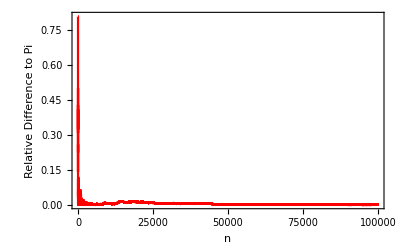

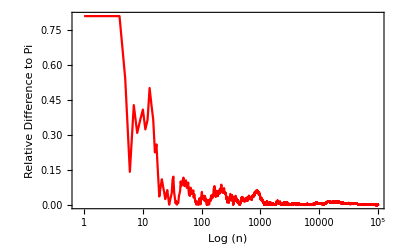

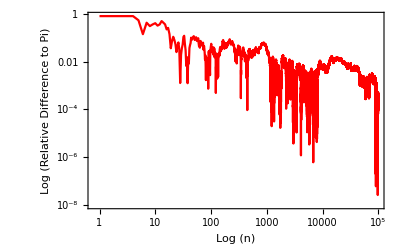

```mathematica
relativediff=MapAt[Abs[#-π]&,average,All];

ListLinePlot[relativediff,PlotRange->Full ,PlotStyle->Red,
Frame->True,FrameLabel->{"n","  \n Relative Difference to Pi"},
RotateLabel->True, LabelStyle->Directive[Black,Bold]]
ListLinePlot[relativediff,PlotRange->Full ,PlotStyle->Red,
ScalingFunctions->{"Log"},
Frame->True,FrameLabel->{"Log (n)","  \n Relative Difference to Pi"},
RotateLabel->True, LabelStyle->Directive[Black,Bold]]
ListLinePlot[relativediff,PlotRange->Full ,PlotStyle->Red,
ScalingFunctions->{"Log","Log"},
Frame->True,FrameLabel->{"Log (n)","  \n Log (Relative Difference to Pi)"},
RotateLabel->True, LabelStyle->Directive[Black,Bold]]
```

### Convergence Plot

```mathematica
(* Plot the estimates along with the mean estimate, and the true value of Pi. *)
GraphicsRow[{Show[ListLinePlot[{gregtable1,gregtable2,gregtable3},PlotRange->{{0,10^5},{3,3.3}},PlotStyle->Green],ListLinePlot[meangreg,PlotStyle->Red],Plot[π,{x,0,10^5},PlotStyle->Black],ImageSize->Large,Frame->True,FrameLabel->{"n","  \n Approximations and Value of Pi"},RotateLabel->True,ImageSize->Large,LabelStyle->Directive[Black,Bold],PlotRange->Full],
	(* Add a legend to the plot. *)
LineLegend[{Green,Red,Black},{"Trials 1 - 3","Mean of the Trials","Pi"}]}]
```

ListLinePlot::lpn: meangreg is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListLinePlot[meangreg,PlotStyle→color],,ImageSize→Large,Frame→True,FrameLabel→{n,  
 Approximations and Value of Pi},RotateLabel→True,ImageSize→Large,LabelStyle→Directive[color,Bold],PlotRange→Full].

-Graphics-